Practical-2: Regula-Falsi Method
Name: Devansh Tyagi
Roll No: 20221416
B.Sc. (Hons.) Computer Science

Regula-Falsi Method: For Given Parameters
Ques-1

x0= 1

x1= 2

Nmax= 100

epsilon= 0.001

f(x):=Cos[x]

1th iteration value is: 1.5649

estimate error is: 1.

2th iteration value is: 1.57098

estimate error is: 0.435096

3th iteration value is: 1.5708

estimate error is: 0.0060742

Return[1.5708]

root is: 1.5708

Estimate error is: 0.000182249

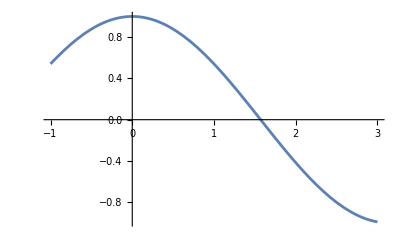

```mathematica
x0 = Input["Enter first guess :"];
x1 = Input["Enter second guess :"];
Nmax = Input["Enter maximum number of iteration :"];
eps = Input["Enter the value of convergence parameter :"];
Print["x0= ", x0];
Print["x1= ", x1];
Print["Nmax= ", Nmax];
Print["epsilon= ", eps];
f[x_] := Cos[x];
Print["f(x):=", f[x]];
If[N[f[x0]*f[x1]] > 0,
	Print["These values do not satisfy the IVP so change the values."],
	For[i=1, i<=Nmax, i++,
		x2 = N[x1-f[x1]*(x1-x0)/(f[x1]-f[x0])];
		If[Abs[x1-x0] < eps, Return[N[x2]],
			Print[i, "th iteration value is: ", N[x2]];
			Print["estimate error is: ", N[x1-x0]]];
		If[f[x2]*f[x1] > 0, x1=x2, x0=x2]]];
Print["root is: ", N[x2]];
Print["Estimate error is: ", N[x1-x0]];
Plot[f[x], {x, -1, 3}]
```

Ques-2

x0= 0

x1= 1

Nmax= 100

epsilon= 0.001

f(x):=-ⅇ^x x+Cos[x]

1th iteration value is: 0.314665

estimate error is: 1.

2th iteration value is: 0.446728

estimate error is: 0.685335

3th iteration value is: 0.494015

estimate error is: 0.553272

4th iteration value is: 0.509946

estimate error is: 0.505985

5th iteration value is: 0.515201

estimate error is: 0.490054

6th iteration value is: 0.516922

estimate error is: 0.484799

7th iteration value is: 0.517485

estimate error is: 0.483078

8th iteration value is: 0.517668

estimate error is: 0.482515

9th iteration value is: 0.517728

estimate error is: 0.482332

10th iteration value is: 0.517748

estimate error is: 0.482272

11th iteration value is: 0.517754

estimate error is: 0.482252

12th iteration value is: 0.517756

estimate error is: 0.482246

13th iteration value is: 0.517757

estimate error is: 0.482244

14th iteration value is: 0.517757

estimate error is: 0.482243

15th iteration value is: 0.517757

estimate error is: 0.482243

16th iteration value is: 0.517757

estimate error is: 0.482243

17th iteration value is: 0.517757

estimate error is: 0.482243

18th iteration value is: 0.517757

estimate error is: 0.482243

19th iteration value is: 0.517757

estimate error is: 0.482243

20th iteration value is: 0.517757

estimate error is: 0.482243

21th iteration value is: 0.517757

estimate error is: 0.482243

22th iteration value is: 0.517757

estimate error is: 0.482243

23th iteration value is: 0.517757

estimate error is: 0.482243

24th iteration value is: 0.517757

estimate error is: 0.482243

25th iteration value is: 0.517757

estimate error is: 0.482243

26th iteration value is: 0.517757

estimate error is: 0.482243

27th iteration value is: 0.517757

estimate error is: 0.482243

28th iteration value is: 0.517757

estimate error is: 0.482243

29th iteration value is: 0.517757

estimate error is: 0.482243

30th iteration value is: 0.517757

estimate error is: 0.482243

31th iteration value is: 0.517757

estimate error is: 0.482243

32th iteration value is: 0.517757

estimate error is: 0.482243

33th iteration value is: 0.517757

estimate error is: 0.482243

34th iteration value is: 0.517757

estimate error is: 0.482243

35th iteration value is: 0.517757

estimate error is: 0.482243

36th iteration value is: 0.517757

estimate error is: 0.482243

37th iteration value is: 0.517757

estimate error is: 0.482243

38th iteration value is: 0.517757

estimate error is: 0.482243

39th iteration value is: 0.517757

estimate error is: 0.482243

40th iteration value is: 0.517757

estimate error is: 0.482243

41th iteration value is: 0.517757

estimate error is: 0.482243

42th iteration value is: 0.517757

estimate error is: 0.482243

43th iteration value is: 0.517757

estimate error is: 0.482243

44th iteration value is: 0.517757

estimate error is: 0.482243

45th iteration value is: 0.517757

estimate error is: 0.482243

46th iteration value is: 0.517757

estimate error is: 0.482243

47th iteration value is: 0.517757

estimate error is: 0.482243

48th iteration value is: 0.517757

estimate error is: 0.482243

49th iteration value is: 0.517757

estimate error is: 0.482243

50th iteration value is: 0.517757

estimate error is: 0.482243

51th iteration value is: 0.517757

estimate error is: 0.482243

52th iteration value is: 0.517757

estimate error is: 0.482243

53th iteration value is: 0.517757

estimate error is: 0.482243

54th iteration value is: 0.517757

estimate error is: 0.482243

55th iteration value is: 0.517757

estimate error is: 0.482243

56th iteration value is: 0.517757

estimate error is: 0.482243

57th iteration value is: 0.517757

estimate error is: 0.482243

58th iteration value is: 0.517757

estimate error is: 0.482243

59th iteration value is: 0.517757

estimate error is: 0.482243

60th iteration value is: 0.517757

estimate error is: 0.482243

61th iteration value is: 0.517757

estimate error is: 0.482243

62th iteration value is: 0.517757

estimate error is: 0.482243

63th iteration value is: 0.517757

estimate error is: 0.482243

64th iteration value is: 0.517757

estimate error is: 0.482243

65th iteration value is: 0.517757

estimate error is: 0.482243

66th iteration value is: 0.517757

estimate error is: 0.482243

67th iteration value is: 0.517757

estimate error is: 0.482243

68th iteration value is: 0.517757

estimate error is: 0.482243

69th iteration value is: 0.517757

estimate error is: 0.482243

70th iteration value is: 0.517757

estimate error is: 0.482243

71th iteration value is: 0.517757

estimate error is: 0.482243

72th iteration value is: 0.517757

estimate error is: 0.482243

73th iteration value is: 0.517757

estimate error is: 0.482243

74th iteration value is: 0.517757

estimate error is: 0.482243

75th iteration value is: 0.517757

estimate error is: 0.482243

76th iteration value is: 0.517757

estimate error is: 0.482243

77th iteration value is: 0.517757

estimate error is: 0.482243

78th iteration value is: 0.517757

estimate error is: 0.482243

79th iteration value is: 0.517757

estimate error is: 0.482243

80th iteration value is: 0.517757

estimate error is: 0.482243

81th iteration value is: 0.517757

estimate error is: 0.482243

82th iteration value is: 0.517757

estimate error is: 0.482243

83th iteration value is: 0.517757

estimate error is: 0.482243

84th iteration value is: 0.517757

estimate error is: 0.482243

85th iteration value is: 0.517757

estimate error is: 0.482243

86th iteration value is: 0.517757

estimate error is: 0.482243

87th iteration value is: 0.517757

estimate error is: 0.482243

88th iteration value is: 0.517757

estimate error is: 0.482243

89th iteration value is: 0.517757

estimate error is: 0.482243

90th iteration value is: 0.517757

estimate error is: 0.482243

91th iteration value is: 0.517757

estimate error is: 0.482243

92th iteration value is: 0.517757

estimate error is: 0.482243

93th iteration value is: 0.517757

estimate error is: 0.482243

94th iteration value is: 0.517757

estimate error is: 0.482243

95th iteration value is: 0.517757

estimate error is: 0.482243

96th iteration value is: 0.517757

estimate error is: 0.482243

97th iteration value is: 0.517757

estimate error is: 0.482243

98th iteration value is: 0.517757

estimate error is: 0.482243

99th iteration value is: 0.517757

estimate error is: 0.482243

100th iteration value is: 0.517757

estimate error is: 0.482243

root is: 0.517757

Estimate error is: 0.482243

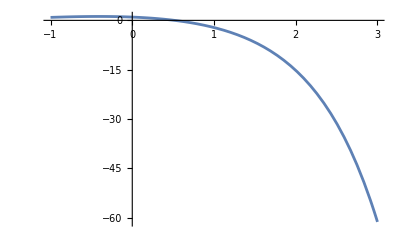

```mathematica
x0 = Input["Enter first guess :"];
x1 = Input["Enter second guess :"];
Nmax = Input["Enter maximum number of iteration :"];
eps = Input["Enter the value of convergence parameter :"];
Print["x0= ", x0];
Print["x1= ", x1];
Print["Nmax= ", Nmax];
Print["epsilon= ", eps];
f[x_] := Cos[x] - x*ⅇ^x;
Print["f(x):=", f[x]];
If[N[f[x0]*f[x1]] > 0,
	Print["These values do not satisfy the IVP so change the values."],
	For[i=1, i<=Nmax, i++,
		x2 = N[x1-f[x1]*(x1-x0)/(f[x1]-f[x0])];
		If[Abs[x1-x0] < eps, Return[N[x2]],
			Print[i, "th iteration value is: ", N[x2]];
			Print["estimate error is: ", N[x1-x0]]];
		If[f[x2]*f[x1] > 0, x1=x2, x0=x2]]];
Print["root is: ", N[x2]];
Print["Estimate error is: ", N[x1-x0]];
Plot[f[x], {x, -1, 3}]
```

Ques-3

x0= 0

x1= 1

Nmax= 100

epsilon= 0.001

f(x):=1-5 x+x^3

1th iteration value is: 0.25

estimate error is: 1.

2th iteration value is: 0.202532

estimate error is: 0.25

3th iteration value is: 0.201654

estimate error is: 0.202532

4th iteration value is: 0.20164

estimate error is: 0.201654

5th iteration value is: 0.20164

estimate error is: 0.20164

6th iteration value is: 0.20164

estimate error is: 0.20164

7th iteration value is: 0.20164

estimate error is: 0.20164

8th iteration value is: 0.20164

estimate error is: 0.20164

9th iteration value is: 0.20164

estimate error is: 0.20164

10th iteration value is: 0.20164

estimate error is: 0.20164

Return[0.20164]

root is: 0.20164

Estimate error is: 2.77556×10^-16

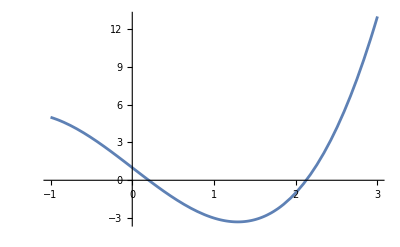

```mathematica
x0 = Input["Enter first guess :"];
x1 = Input["Enter second guess :"];
Nmax = Input["Enter maximum number of iteration :"];
eps = Input["Enter the value of convergence parameter :"];
Print["x0= ", x0];
Print["x1= ", x1];
Print["Nmax= ", Nmax];
Print["epsilon= ", eps];
f[x_] := x^3-5x+1;
Print["f(x):=", f[x]];
If[N[f[x0]*f[x1]] > 0,
	Print["These values do not satisfy the IVP so change the values."],
	For[i=1, i<=Nmax, i++,
		x2 = N[x1-f[x1]*(x1-x0)/(f[x1]-f[x0])];
		If[Abs[x1-x0] < eps, Return[N[x2]],
			Print[i, "th iteration value is: ", N[x2]];
			Print["estimate error is: ", N[x1-x0]]];
		If[f[x2]*f[x1] > 0, x1=x2, x0=x2]]];
Print["root is: ", N[x2]];
Print["Estimate error is: ", N[x1-x0]];
Plot[f[x], {x, -1, 3}]
```